{{φ→InterpolatingFunction[{{…, -20., 20., …}, {0., 15.}}, <>],ϕ→InterpolatingFunction[{{…, -20., 20., …}, {0., 15.}}, <>]}}

φ Field Amplitude:

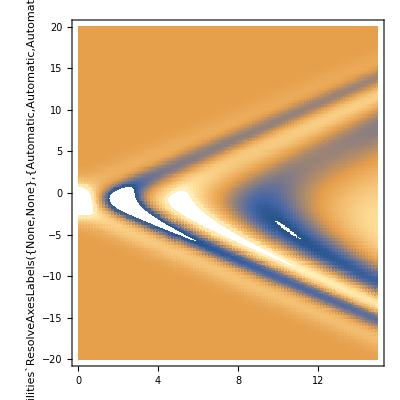

ϕ Field Amplitude:

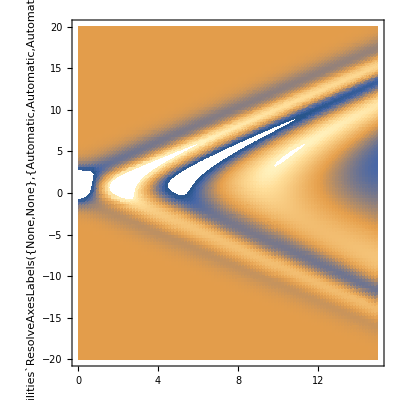

φ and ϕ Field Amplitudes:

Hamiltonian Density:

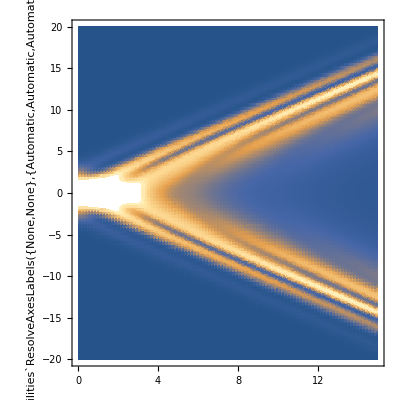

```mathematica
λ=1;
a=1;
time=15;
X=20;
V=λ/2*(φ[x,t]^2+ϕ[x,t]^2)^2;
ℒ=1/2*(D[φ[x,t],t]^2-D[φ[x,t],x]^2)+1/2*(D[ϕ[x,t],t]^2-D[ϕ[x,t],x]^2)-V;
ℋ=1/2*(D[φ[x,t],t]^2+D[φ[x,t],x]^2)+1/2*(D[ϕ[x,t],t]^2+D[ϕ[x,t],x]^2)+V;
Needs["VariationalMethods`"]
eqs=EulerEquations[ℒ,{φ[x,t],ϕ[x,t]},{x,t}];
s=NDSolve[{eqs,φ[x,0]==Exp[-(x+a)^2/4],Derivative[0,1][φ][x,0]==0,φ[-X,t]==φ[X,t],ϕ[x,0]==-Exp[-(x-a)^2/4],Derivative[0,1][ϕ][x,0]==0,ϕ[-X,t]==ϕ[X,t]},{φ,ϕ},{x,-X,X},{t,0,time}]
"φ Field Amplitude:"
DensityPlot[Evaluate[φ[x,t]/.s],{t,0,time},{x,-X,X},WorkingPrecision->20,PlotPoints->100]
"ϕ Field Amplitude:"
DensityPlot[Evaluate[ϕ[x,t]/.s],{t,0,time},{x,-X,X},WorkingPrecision->20,PlotPoints->100]
"φ and ϕ Field Amplitudes:"
Animate[Show[Plot[{φ[x,t]/.s,ϕ[x,t]/.s},{x,-X,X},PlotRange->{-1,1},Filling->Axis],BoxRatios->Automatic],{t,0,time},AnimationRate->1, AnimationRunning->False,RefreshRate->30]
"Hamiltonian Density:"
DensityPlot[Evaluate[ℋ/.s],{t,0,time},{x,-X,X},WorkingPrecision->20,PlotPoints->100]
```